## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data["student"]=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data["student"],5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

### Fitting routines

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n];
(* For testing *)
(* I had some concern that the original method was not finding the global minimu *)
bkt2[nn_][n_,{a_,pg_,ps_}]:=1-ps-(1-ps-pg) a^(n/nn);
half[n_,{}]:=1/2;
```

```mathematica
stepFit[data_,i_]:=Block[{l0=Count[Take[data,i],0],l1=Count[Take[data,i],1],u0=Count[Drop[data,i],0],u1=Count[Drop[data,i],1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];logLike]
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{logLike=stepFit[data,i-1]},If[logLike>best,best=logLike;lBest=i]],{i,Length[data]}];If[Length[data]≥3,2*3-2*N[best]]]
```

```mathematica
selectFitable[x_]:=Block[{data=Drop[x,3]},Length[data]≥3 && Count[data,0]!=0 && Count[data,1]!=0]
(* Akaike weights for step model when all L are equally probable. *)
avgWeights[n_]:=Table[If[i==1,Exp[1],1],{i,n}]/(Exp[1]+n-1)
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle -Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i-1,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0]==0 || Count[data,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

```mathematica
bkt2Constraints[x_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&a≥Exp[-Length[x] delta] && a<1-Exp[-delta]]
```

Correction to get AIC_c

```mathematica
aicCorrection[k_,n_]:=2 k (k+1)/(n-k-1)
```

### Generate random data and table of AIC' s

Make random data, 50 % correct

```mathematica
data["random"]=Table[Join[{Null,Null,Null},Table[RandomInteger[],{10}]],{1000}];
```

Make random data, span space, with 50 % correct

```mathematica
data["even",n_]:=Table[Join[{Null,Null,Null},IntegerDigits[i-1,2,n]],{i,2^n}];
```

```mathematica
data["random",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},Table[RandomInteger[],{Length[Drop[#,3]]}]]&,data["student"]],{n}],1];
```

```mathematica
data["reorder",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},RandomSample[Drop[#,3]]]&,data["student"]],{n}],1];
```

Make exponential data

```mathematica
data["exponential"]=Table[Join[{Null,Null,Null},Block[{a=Random[],b=Random[],c=Random[],n=100},Table[If[Random[]<a+(b-a) c^( i/n),1,0],{i,n}]]],{100}];
```

### Generate full table of AIC' s

```mathematica
TableForm[allValues=Map[{#[[1]],#[[3]],Length[Drop[#,3]],Print[#[[1]]," logistic ",#[[3]]];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],stepFit[Drop[#,3]],Print[#[[1]]," bkt ",#[[3]]];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],maxer[bkt2[Length[Drop[#,3]]],{a,pg,ps},bkt2Constraints,Drop[#,3]],-2*N[logProb[half,{},Drop[#,3]]]}&,data]]
```

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

$Aborted

```mathematica
Save["fitAll.m",allValues]
```

### Step function model: Plot Akaike weights.

#### Determine "peakiness" of Akaike weight vs. L for log data

```mathematica
Clear[dataWeights];dataWeights[set__]:=dataWeights[set]=Map[Function[x,x/Apply[Plus,x]][Table[Block[{aic=2*If[i==1,1,2]-2.*stepFit[Drop[#,3],i-1]},Exp[-aic/2]],{i,Length[Drop[#,3]]}]]&,Select[data[set],selectFitable]];
```

```mathematica
stats[set__]:=Block[{xx=Map[#/avgWeights[ Length[#]]&,dataWeights[set]],xxx},
xxx=Flatten[xx];{Length[xx],StandardDeviation[Log[xxx]],Sqrt[Total[Log[xxx]^2]/(Length[xxx]-1)],
Mean[Select[xxx,(#>1)&]],StandardDeviation[Select[xxx,(#>1)&]],
Mean[1/Select[xxx,(#<1)&]],StandardDeviation[1/Select[xxx,(#<1)&]]}]
```

```mathematica
stats["student"]
```

{783,0.815087,0.867163,2.15164,1.88576,2.66319,4.97013}

```mathematica
Table[stats["reorder",i],{i,10}]
```

{{783,0.621724,0.641758,1.7639,1.3069,1.89023,2.23537},{1566,0.611519,0.632152,1.85328,1.10664,1.78932,1.30421},{2349,0.629541,0.650212,1.80952,1.33242,1.90808,2.63166},{3132,0.655962,0.680308,1.86616,1.61001,2.0721,4.47116},{3915,0.673146,0.698411,1.83783,1.52967,2.07786,3.52121},{4698,0.633863,0.655192,1.80928,1.29724,1.90626,3.10449},{5481,0.654155,0.675805,1.8242,1.28062,2.19608,8.92157},{6264,0.638545,0.661007,1.83648,1.31831,1.93695,2.79125},{7047,0.647608,0.670766,1.82591,1.41914,1.97852,3.2448},{7830,0.667193,0.691229,1.85221,1.37601,2.23416,8.57241}}

```mathematica
Table[stats["random",i],{i,10}]
```

{{948,0.852403,0.901368,2.01031,1.81522,3.51303,14.9001},{1886,0.739715,0.773395,1.88361,1.67778,3.41993,17.4807},{2818,0.651115,0.683565,1.92019,1.93516,2.29136,25.1865},{3771,0.64361,0.676842,1.92113,1.80405,1.91156,2.26742},{4722,0.740626,0.783727,2.01417,2.44937,2.43489,4.66629},{5696,0.738129,0.78105,2.00247,2.36881,2.53816,20.9139},{6638,0.683607,0.720561,1.95192,2.24106,2.11837,3.79468},{7532,0.735612,0.779624,1.98671,2.77486,2.32734,3.8935},{8500,0.704379,0.744266,1.98965,2.33374,2.23091,4.35227},{9465,0.669965,0.705347,1.94651,2.16432,2.07081,3.49772}}

Need to do this in Mma 8

```mathematica
Histogram[{Flatten[Map[#/avgWeights[ Length[#]]&,dataWeights["random",10]]],
Flatten[Map[#/avgWeights[ Length[#]]&,dataWeights["reorder",10]]],Flatten[Map[#/avgWeights[ Length[#]]&,dataWeights["student"]]]},{"Log",50},"Probability",PlotRange->All]
```

Log binning does not work in Mma 7

```mathematica
Histogram[Log[{Flatten[Map[#/avgWeights[ Length[#]]&,dataWeights["random",10]]],
Flatten[Map[#/avgWeights[ Length[#]]&,dataWeights["reorder",10]]],Flatten[Map[#/avgWeights[ Length[#]]&,dataWeights["student"]]]}],50,"Probability",PlotRange->{{-4,3},All},Axes->False,Frame->True]
```

-Graphics-

```mathematica
Histogram[{Flatten[Map[Select[#/avgWeights[ Length[#]],Function[x,x>1]]&,dataWeights["random",10]]],
Flatten[Map[Select[#/avgWeights[ Length[#]],Function[x,x>1]]&,dataWeights["reorder",10]]],Flatten[Map[Select[#/avgWeights[ Length[#]],Function[x,x>1]]&,dataWeights["student"]]]},Automatic,"Probability",Axes->False,Frame->True,PlotRange->{{1,10},All}]
```

-Graphics-

For points below 1, take reciprocol and histogram

```mathematica
Histogram[{Flatten[Map[Select[1/(#/avgWeights[ Length[#]]),Function[x,x>1]]&,dataWeights["random",10]]],
Flatten[Map[Select[1/(#/avgWeights[ Length[#]]),Function[x,x>1]]&,dataWeights["reorder",10]]],Flatten[Map[Select[1/(#/avgWeights[ Length[#]]),Function[x,x>1]]&,dataWeights["student"]]]},Automatic,"Probability",Axes->False,Frame->True,PlotRange->{{1,10},All}]
```

-Graphics-

```mathematica
hist[set__]:=Histogram[Flatten[Map[Rest,dataWeights[set]]],"Log",PlotRange->All]
```

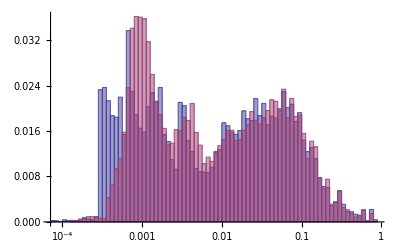

```mathematica
Histogram[{Flatten[Map[Rest,dataWeights["student"]]],Flatten[Map[Rest,dataWeights["reorder",10]]]},"Log","Probability",PlotRange->All]
```

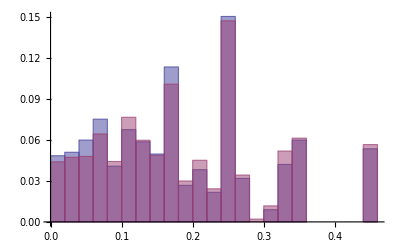

```mathematica
Histogram[{Flatten[Map[First,dataWeights["student"]]],Flatten[Map[First,dataWeights["reorder",10]]]},Automatic,"Probability",PlotRange->All]
```

```mathematica
Histogram[Map[Block[{delta=#[[1]]-#[[2]]},Sqrt[delta.delta]]&,Transpose[{dataWeights["student"],dataWeights["reorder"]}]]]
```

-Graphics-

Real Student data

-Graphics-

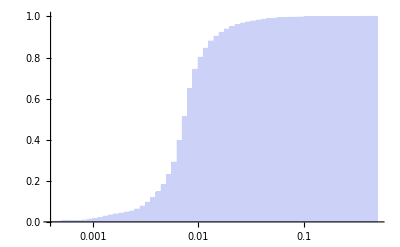

```mathematica
random data
```

```mathematica
Histogram[Flatten[Map[(#*Length[#])&,xxx]],PlotRange->{{0,2},All}]
```

-Graphics-

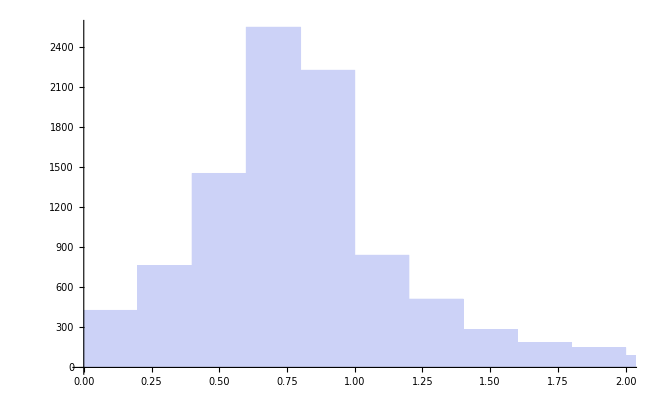

```mathematica
random data
```

```mathematica
rescaler[data_]:=Block[{n=Length[data]},Table[{(i-1)/(n-1),n*data[[i]]},{i,n}]]
```

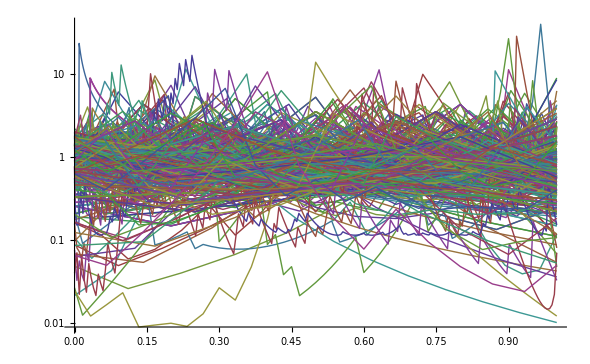

```mathematica
ListLogPlot[Map[rescaler,xxx],Joined->True,PlotRange->All]
```

#### Example KC for paper

```mathematica
data1={1,0,0,1,1,1,0,1,0,1};
```

```mathematica
data1={0,0,0,1,1,0,1,1};
```

```mathematica
aics=Table[{i,N[2*If[i==1,1,2]-2*stepFit[data1,i-1]]},{i,Length[data1]}]
```

{{1,13.0904},{2,13.5607},{3,11.6382},{4,9.00402},{5,12.9974},{6,14.5492},{7,11.6382},{8,13.5607}}

```mathematica
weights1=Function[x,x/Apply[Plus,x]][N[Table[Block[{aic=2*If[i==1,1,2]-2*stepFit[data1,i-1]},Exp[-aic/2]],{i,Length[data1]}]]]
```

{0.0626582,0.0495269,0.129514,0.483407,0.0656404,0.030213,0.129514,0.0495269}

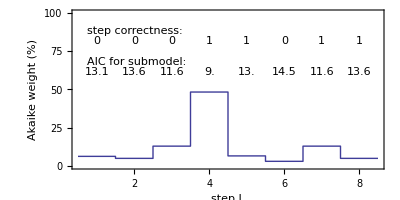

```mathematica
stepWeightsPlot=Block[{n=Length[data1],yt=85,y2=65},ListPlot[Flatten[Table[{{i-1/2,#},{i+1/2,#}}&[weights1[[i]]*100],{i,n}],1],Epilog->{Text["step correctness:",{0.75,yt},{-1,-1}],Table[Text[data1[[i]],{i,yt},{0,1}],{i,n}],
Text["AIC for submodel:",{0.75,y2},{-1,-1}],
	Map[Text[Round[#[[2]],0.1],{#[[1]],y2},{0,1}]&,aics]},PlotRange->{{1/2,n+1/2},{0,100}},
Joined->True,
FrameLabel->{"step L","Akaike weight (%)"},BaseStyle->{FontSize->12}, AspectRatio->1/2,Axes->False,Frame->True]]
```

```mathematica
Export["step-weights.eps",stepWeightsPlot]
```

step-weights.eps

### Stuff

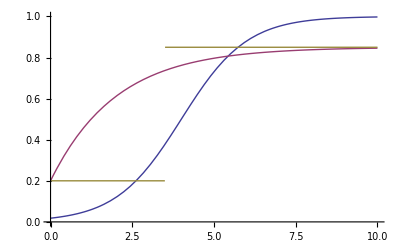

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

Distribution of KC opportunity counts

```mathematica
nlist=Map[Length[Drop[#,3]]&,data];
```

```mathematica
{Median[nlist],N[Mean[nlist]],Median[Select[nlist,#≥10&]],N[Mean[Select[nlist,#≥10&]]]}
```

{3,15.88,17,101.176}

```mathematica
Histogram[nlist,"Log","LogCount"]
```

-Graphics-

### Analyze

Logistic, step model, Baysian Knowledge Tracing

```mathematica
Get["fitAll.m"];
```

```mathematica
Get["fitRandomData.m"];
```

```mathematica
Get["fitBktData.m"];
```

```mathematica
allValues[[42]]
```

{Null,Null,100,142.377,140.46,143.152,144.399,138.629}

```mathematica
Length[cutValues=Select[allValues,#[[3]]≥10&]]
```

100

```mathematica
{Length[Union[Map[First,cutValues]]],Length[Union[Map[#[[2]]&,cutValues]]]}
```

{1,1}

```mathematica
aics=Map[{#[[4]]+aicCorrection[2,#[[3]]],#[[5]]+aicCorrection[3,#[[3]]],Min[#[[6]],#[[7]]]+aicCorrection[3,#[[3]]]}&,cutValues];
```

```mathematica
akaikeWeights=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,aics];
```

```mathematica
akaikeRawWeights=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,Map[Drop[#,3]&,cutValues]];
```

```mathematica
Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights]]
```

BKT generated data

{{0.31447,0.291953,0.00137773},{0.52383,0.545306,0.0017625},{0.146817,0.162741,0.000865266}}

random generated data

{{0.261987,0.24624,0.00120186},{0.568935,0.606061,0.00166846},{0.131925,0.1477,0.000839937}}

real data

{{0.519307,0.498869,0.000694742},{0.365428,0.377065,0.000714023},{0.121277,0.124065,0.00020089}}

```mathematica
Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeRawWeights]]
```

BKT generated data

{{0.229796,0.230544,0.00112984},{0.442106,0.476069,0.00193064},{0.106252,0.12072,0.000805316},{0.10403,0.111788,0.000572076},{0.000156314,0.0608794,0.00132656}}

random generated data

{{0.106209,0.118937,0.000602622},{0.327748,0.369046,0.00206234},{0.0572125,0.0766074,0.000551509},{0.0458182,0.0586759,0.00043521},{0.411899,0.376734,0.00208807}}

real data

{{0.273235,0.295426,0.000563282},{0.332109,0.346379,0.000650819},{0.10303,0.106448,0.000190688},{0.103984,0.106556,0.000185926},{0.0215907,0.145191,0.000742492}}

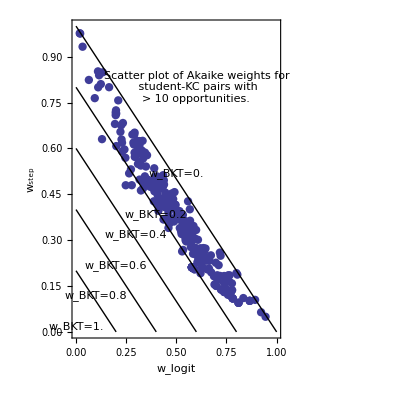

```mathematica
scatterWeights=ListPlot[Map[Take[#,2]&,akaikeWeights],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n student-KC pairs with\n> 10 opportunities.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->{FontSize->12}]
```

```mathematica
Export["scatter-weights.eps",scatterWeights]
```

scatter-weights.eps

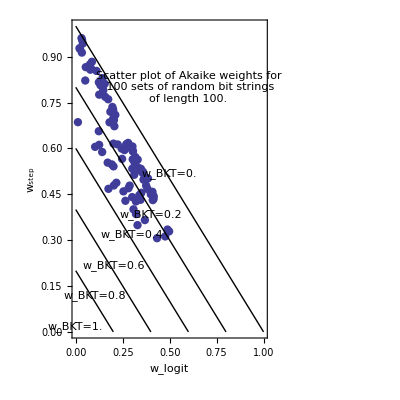

```mathematica
scatterRandomWeights=ListPlot[Map[Take[#,2]&,akaikeWeights],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n 100 sets of random bit strings\nof length 100.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->{FontSize->12}]
```

```mathematica
Export["scatter-random-weights.eps",scatterRandomWeights]
```

scatter-random-weights.eps

```mathematica
Histogram3D[Map[Take[#,2]&,akaikeWeights],{{0,1,0.02},{0,1,0.02}},PlotRange->{{0,1},{0,1},All}]
```

-Graphics3D-